## Pi Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pi=RealDigits[Pi,10,10000][[1,2;;]];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[pi]
```

{0.192238,0.949378}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[pi];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|2→2405,5→971,14→87,16→61,8→356,3→2088,4→1503,7→503,10→225,17→63,12→159,6→679,11→201,9→301,13→113,23→16,25→12,18→47,15→63,20→24,19→35,24→10,21→16,22→25,27→6,28→10,26→4,29→5,31→3,32→1,33→2,30→2,35→1,37→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

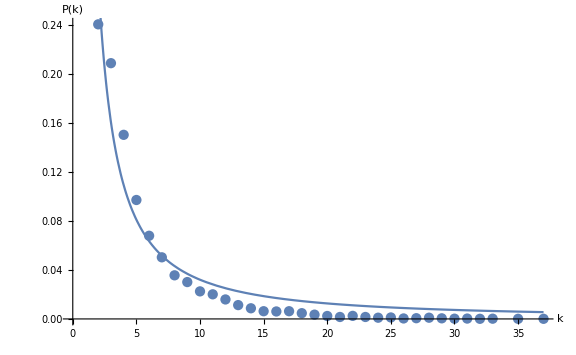
{{C→0.699806,γ→1.33965},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[pi];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|2→3879,3→2224,6→628,4→1382,5→901,8→238,7→399,10→101,9→149,11→53,16→1,13→11,12→28,14→3,1→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

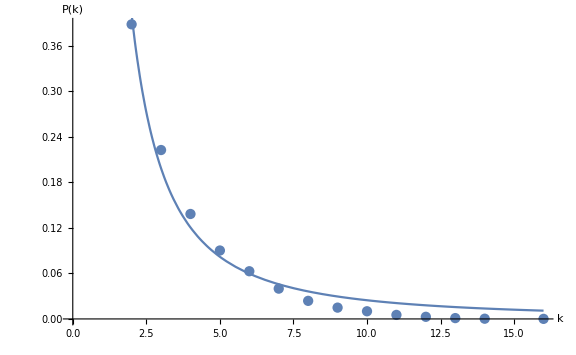
{{{1.33302,0.248704},{1.73399,0.195355}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```